```mathematica
Quit
```

```mathematica
$Assumptions = Dif > 0 && t > 0
```

Dif>0&&t>0

```mathematica
EFP=D[f[t,x],t]+μ D[f[t,x],x]-Dif D[f[t,x],x,x]
```

μ f^(0,1)[t,x]-Dif f^(0,2)[t,x]+f^(1,0)[t,x]

```mathematica
f[t_,x_]=1/(4π Dif t)^(1/2)Exp[-(x-x0-μ t)^2/(4 Dif t)]
```

(ⅇ^(-(x-x0-t μ)^2/(4 Dif t)))/(2 √π √(Dif t))

Checkeo de normalización: La probabilidad de que la partícula esté en algún lugar debe ser 1

```mathematica
Integrate[f[t,x],{x,-Infinity,+Infinity}]
```

1

Checkeo de que es solución

```mathematica
EFP//FullSimplify
```

0

Promedio

```mathematica
Integrate[x f[t,x],{x,-Infinity,+Infinity}]
```

x0+t μ

Desviación estandard^2 Calculamos < x^2>-<x>^2

```mathematica
Integrate[x^2 f[t,x],{x,-Infinity,+Infinity}]-(Integrate[x f[t,x],{x,-Infinity,+Infinity}])^2
```

2 Dif t

```mathematica
f[t,x]/.{x0->0,Dif->1,μ->0}
```

(ⅇ^(-x^2/(4 t)))/(2 √π √t)

```mathematica
Table[(ⅇ^(-x^2/(4 t)))/(2 √π √t),{t,0.1,0.5,0.1}]
```

{0.892062 ⅇ^(-2.5 x^2),0.630783 ⅇ^(-1.25 x^2),0.515032 ⅇ^(-0.833333 x^2),0.446031 ⅇ^(-0.625 x^2),0.398942 ⅇ^(-0.5 x^2)}

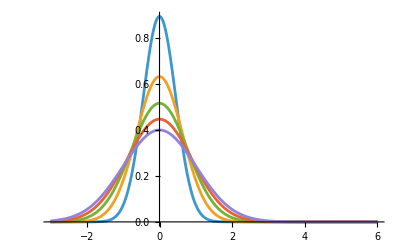

```mathematica
Plot[{0.8920620580763855 ⅇ^(-2.5 x^2),0.6307831305050401 ⅇ^(-1.25 x^2),0.5150322693642527 ⅇ^(-0.8333333333333333 x^2),0.44603102903819275 ⅇ^(-0.625 x^2),0.39894228040143265 ⅇ^(-0.5 x^2)},{x,-3,6}]
```

```mathematica
Manipulate[Plot[(ⅇ^(-x^2/(4 t)))/(2 √π √t),{x,-2,2},PlotRange->{{-2,2},{0,5}}],{t,1/1000,1/10}]
```

General::munfl: Exp[-999.918] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 
   Exp[-999.918] is too small to represent as a normalized machine number;
     precision may be lost.

```mathematica
Quit
```

Fotos de la distribución a distintos tiempos, para ν=1, d=1,x0=1

```mathematica
{ν=1,d=1,x0=1}
```

{1,1,1}

```mathematica
f[t_,x_]=1/(4π d t)^(1/2)Exp[(-(x-x0-ν t)^2)/(4 d t)]
```

(ⅇ^(-(-1-t+x)^2/(4 t)))/(2 √π √t)

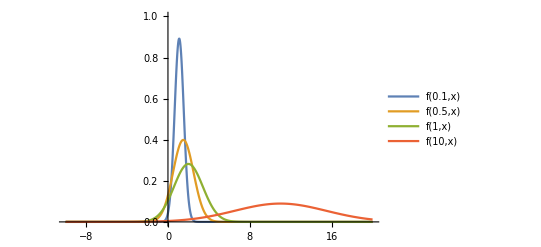

```mathematica
Plot[{f[0.1,x],f[0.5,x],f[1,x],f[10,x]},{x,-10,20},PlotRange->{{-10,20},{0,1}},PlotLegends->"Expressions"]
```

```mathematica
Quit
```

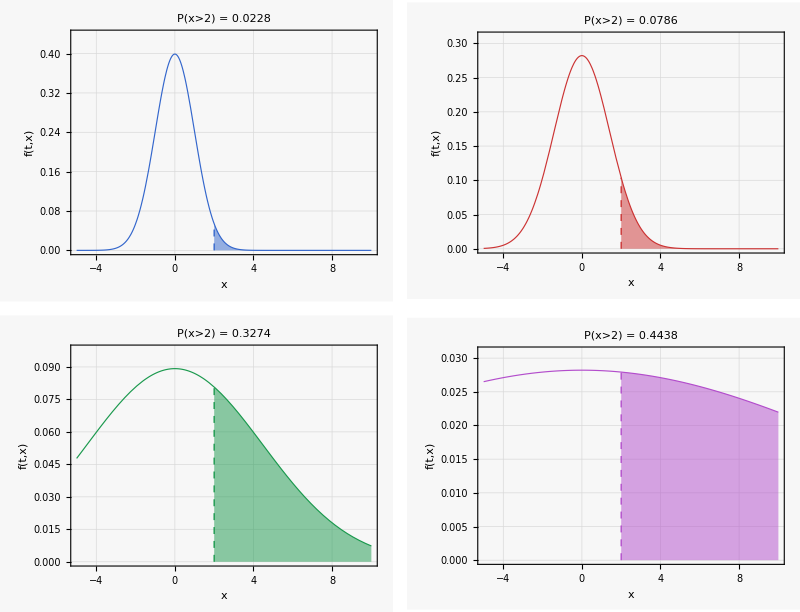
Diffusion Distribution  f(t,x)
Parameters:  d = 1,  x₀ = 0,  v = 0

-Graphics-

t | Peak Position | Peak Height | P(x > 2)
0.5 | 0.000 | 0.3989 | 0.02275
1. | 0.000 | 0.2821 | 0.07865
10 | 0 | 1/(2 √(10 π)) | 0.32740
100 | 0 | 1/(20 √π) | 0.44380

```mathematica
(*Parameters*)d=1;
x0=0;
v=0;

f[t_,x_]:=(1/(4 π d t)^(1/2)) Exp[-(x-x0-v t)^2/(4 d t)]

times={0.5,1.0,10,100};
colors={RGBColor[0.2,0.4,0.8],RGBColor[0.8,0.2,0.2],RGBColor[0.1,0.6,0.3],RGBColor[0.7,0.3,0.8]};

(*Integrate the right tail from x=2 to infinity*)
areas=Table[NIntegrate[f[t,x],{x,2,Infinity}],{t,times}];

plots=Table[Module[{ymax,shadedPts,shadedPoly},ymax=1.1 Max[Table[f[times[[i]],x],{x,-5,10,0.05}]];
(*Sample the tail from x=2 to x=10 (effectively infinity for display)*)shadedPts=Table[{x,f[times[[i]],x]},{x,2,10,0.05}];
shadedPoly=Polygon[Join[{{2,0}},shadedPts,{{10,0}}]];
Show[Plot[],{x,-5,10},PlotStyle->{colors[[i]],Thickness[0.003]},PlotRange->{{-5,10},{0,ymax}}],(*Tail polygon shading*)Graphics[{Opacity[0.5],colors[[i]],shadedPoly,Opacity[1],Dashed,colors[[i]],Line[{{2,0},{2,f[times[[i]],2]}}]}],Frame->True,FrameLabel->{{"f(t,x)",None},{"x",Style["t = "<>ToString[times[[i]]],14,Bold,colors[[i]]]}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotLabel->Style["P(x>2) = "<>ToString[NumberForm[areas[[i]],{4,4}]],12,Bold,colors[[i]]],Background->GrayLevel[0.97],ImageSize->280]],{i,1,4}];

table=Grid[Join[{{Style["t",Bold,13],Style["Peak Position",Bold,13],Style["Peak Height",Bold,13],Style["P(x > 2)",Bold,13]}},Table[{Style[times[[i]],colors[[i]],12],Style[NumberForm[x0+v times[[i]],{4,3}],12],Style[NumberForm[1/(4 π d times[[i]])^(1/2),{4,4}],12],Style[NumberForm[areas[[i]],{4,5}],colors[[i]],Bold,12]},{i,1,4}]],Frame->All,FrameStyle->GrayLevel[0.7],Spacings->{2,1},Background->{{},{GrayLevel[0.88],GrayLevel[0.97],GrayLevel[0.97],GrayLevel[0.97],GrayLevel[0.97]}}];

Column[{Style["Diffusion Distribution  f(t,x)",18,Bold,GrayLevel[0.2]],Style["Parameters:  d = "<>ToString[d]<>",  x₀ = "<>ToString[x0]<>",  v = "<>ToString[v],12,GrayLevel[0.5]],Spacer[10],GraphicsGrid[{plots[[{1,2}]],plots[[{3,4}]]},Spacings->{10,10}],Spacer[10],table},Alignment->Center]
```